# Real Analysis, Lecture 14

## The Intermediate Value Property

## Derivatives satisfy the Intermediate Value Property (even though certain derivatives may not be continuous)

```mathematica
f[x_]:=Piecewise[{{x^2*Sin[1/x], x≠0}, {0, x=0}}]
```

```mathematica
f'[0]
```

Set::write: Tag Slot in #1 is Protected.

0

Set::write: Tag Slot in #1 is Protected.

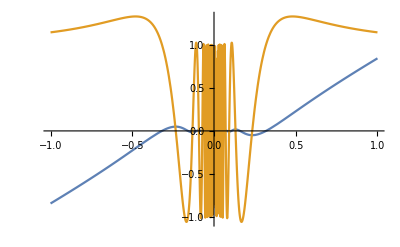

```mathematica
Plot[{f[x],f'[x]},{x,-1,1}]
```

## Uniform Continuity

```mathematica
g[x_]:=x^2;h[x_]:=1/x;Invg[x_]:=√x;Invh[x_]:=h[x];Manipulate[Show[Plot[f[x],{x,0,2},PlotStyle->{Thick,Black}],Graphics[{Thick,Red,Line[{{0,f[c]+ϵ},{Invf[f[c]+ϵ],f[c]+ϵ}}]}],Graphics[{Thick,Red,Line[{{0,f[c]-ϵ},{Invf[f[c]-ϵ],f[c]-ϵ}}]}],Graphics[{Thick,Green,Line[{{0,f[c]},{c,f[c]},{c,0}}]}],Graphics[{Thick,Blue,Line[{{c-δ,0},{c-δ,f[c-δ]}}]}],Graphics[{Thick,Blue,Line[{{c+δ,0},{c+δ,f[c+δ]}}]}],PlotRange->{-1,5},AspectRatio->1],{f,{g,h}},{Invf,{Invg,Invh}},{c,.51,2},{ϵ,.2,.01},{δ,.5,.001}]
```

## Prove that f(x)=1/x is not uniformly continuous on (0,1)

## The Main "Uniform Continuity Theorem"

## Prove that f(x)=sin(x^2) is not uniformly continuous on ℝ

## Monotone Functions are "nice"

### One-sided Limits Exist at Every Point

### The Set of Discontinuities is Countable

### They are Differentiable "Almost Everywhere"

### They are Riemann Integrable

## The Variation of a Function and Functions of Bounded Variation

```mathematica
f[x_]:=Sin[x]+1/2;a=0;b=2π;
```

```mathematica
V[x_]:=Piecewise[{{Abs[f[x]-f[0]], a≤x<π/2}, {Abs[f[π/2]-f[0]]+Abs[f[x]-f[π/2]], π/2≤x<(3π)/2}, {Abs[f[π/2]-f[0]]+Abs[f[(3π)/2]-f[π/2]]+Abs[f[x]-f[(3π)/2]], (3π)/2≤x≤b}}];
```

```mathematica
f1[x_]:=V[x];f2[x_]:=f1[x]-f[x];
```

```mathematica
Plot[{f[x],f1[x],f2[x]},{x,a,b},PlotStyle->{{Thick,Purple},{Thick,Red},{Thick,Blue}}]
```

## Derivatives